```mathematica
ME314 Final Project;
FeiyuChen;
This is the __main__ file of my project;
```

```mathematica
(*Quit[]*)
(*Open and run all other Mathematica scripts*)
(*myOpenFile[filename_]:=Module[{nb1},nb1=NotebookOpen[NotebookDirectory[]<>"/"<>filename];
     SelectionMove[nb1,All,Notebook];
     SelectionEvaluate[nb1]
]
myOpenFile["funcs_math.nb"];
myOpenFile["funcs_assist.nb"];
myOpenFile["funcs_main.nb"];*)
```

```mathematica
(* ------------------------------------------- *)
(*Put your code here to create links system*)
CreateObjects:=Module[{},

(* ------ Output of createLink ------
The link class returned by createLink has 5 elements;
{T,pFront,pBack,TFront,TBack};

You need to access them by index;
IdxT=1;IdxPFront=2;IdxPBack=3;IdxTFront=4;IdxTBack=5;
Such as:
link1=createLink3DOFpp[p0,p1]
link1[[IdxTFront]]
*)


(* --------------------------------*)
(* Example 1: A flying polygon, with NumberOfEdges *)
nthGroup= 1;
initRandVelocity=2.0;

p0={-0.3,0}; (*set the pose of the first link*)
p1={0.3,0.3};
l=CalcDistpp[p0,p1];

NumberOfEdges=3;
linki=createLink3DOFpp[p0,p1];
For[cnt=1,cnt≤NumberOfEdges-1,cnt=cnt+1,
linki=createLink0DOFgθl[linki[[IdxTFront]],2*Pi/NumberOfEdges,l];
];

(* Example 2: 2-link, with a fixed origin *)
nthGroup=2;
initRandVelocity=3.0;

gFix=Trans4[-1,1.8];

createVertex[gFix];
linki=createLink1DOFgθl[gFix,-Pi/2,1.5];
linki=createLink1DOFgθl[linki[[IdxTFront]],-Pi/2,1];

(* Example 3: 2-links, the start point has a fixed height  *)

(*nthGroup=3;
initRandVelocity=0;

p0={1.4,1.7}; (*set the pose of the first link*)
p1={1.7,1.7};

linki=createLink3DOFpp[p0,p1];
addConstraint[linki[[IdxPBack]][[2]]==0];(*Fix origin y*)

linkj=createLink1DOFgθl[linki[[IdxTFront]],-Pi/2,0.5];
*)

(* Example 4: A square wall with 4 edges *);
nthGroup=10;
pWalls={{-3,+3},{+3,0},{+3,-3},{-3,-2}};
AppendTo[pWalls,pWalls[[1]]];
For[i=1,i≤4,i++,
createLink0DOFpp[pWalls[[i]],pWalls[[i+1]]]
];

(* Example 5: Walls in the middle *)
createLink0DOFpp[{-1,-2},{-1,-1}];

];
```

```mathematica
(* Set up all things *)
mainResetVars;
CreateObjects;
RemoveDuplicateVertexs;

Print["\nStart solving EL-eqs..."];
mainSolveELeqs;
Print["Finished solving EL-eqs..."];

Print["\nStart setting impacts ..."];
SetUpImpacts[];
Print["Finished setting impacts ..."];
```

Start solving EL-eqs...

Finished solving EL-eqs...

Start setting impacts ...

Finished setting impacts ...

Part::partw: Part 76 of {1.3,2.498×10^-16,0.939149,2.7,2.81122,«41»,-1.23732,3.29407,4.,0.3,«25»} does not exist.

Part::partw: Part 76 of {«1»} does not exist.

LessEqual::nord: Invalid comparison with 0.554423-4.96507×10^-17 ⅈ attempted.

LessEqual::nord: Invalid comparison with -0.27775+6.97728×10^-17 ⅈ attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

Part::partw: Part 76 of {True,False,True,False,True,True,False,False,False,True,«31»,False,True,True,False,False,False,True,False,0≤5.+3.39908×10^-32 ⅈ&&5.+3.39908×10^-32 ⅈ≤1.,«25»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

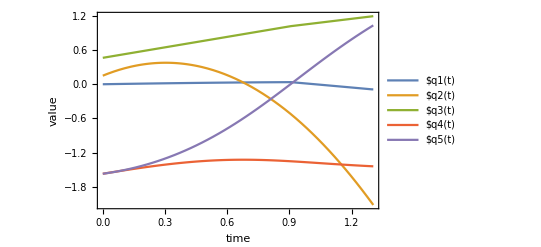

```mathematica
(* Set up params for NDSolve *)
timeend=10;(* total simulation time *)
MAXIMPACTTIMES=200;
impactDetectionError=0.1;
intergrationMaxStepSize=0.01;
ifprint=False;

ddqSolve=TurnToEq[ddqs,EQ[[1,;;,2]]];

(* NDsolve and Play simulation *)
{end,data,bounces}=mainNDSolveSimulation[qsInit,dqsInit];

(* Plot *)

plotVariablesValues
plotAnimation
```